# Reflect

Author Information

Wilfrid S. Kendall

Statistics, University of Warwick,

Coventry CV4 7 AL, UK .

Purpose

This is a Mathematica notebook that demonstrates a pretty fact about coupled pairs of Brownian motions reflecting off a half-plane, and coupled by reflection. The result is easy to prove directly once known: however it is indeed the case that it was discovered using Itovsn3 (in fact in its REDUCE implementation).

IMPORTANT

This notebook assumes nothing has been previously defined. Quit Mathematica and reload if this is not the case!

Load package

```mathematica
Needs["FernandoDuarte`Itovsn3`"]
```

## Set up semimartingales including local times

Now we set up Itovsn3 with time t as the basic semimartingale and add a two-dimensional Brownian motion:

```mathematica
ItoReset[t,dt]
BrownBasis[{A,B},{A0,B0}]
```

Itovsn3  resetting ...
Itovsn3  initialized
with time semimartingale t
and time differential dt

Next step is to introduce the two local times, one for each of the two coupled two-dimensional reflecting Brownian motions.

```mathematica
Introduce[L,dL]
AddQuadVar[dL^2,0];
AddQuadVar[dL dA,0];
AddQuadVar[dL dB,0];
AddDrift[dL,dL];
AddFixed[0,L,L0];
Introduce[H,dH]
AddQuadVar[dH^2,0];
AddQuadVar[dH dA,0];
AddQuadVar[dH dB,0];
AddQuadVar[dH dL,0];
AddDrift[dH,dH];
AddFixed[0,H,H0];
```

{dL,dB,dA,dt}

{dH,dL,dB,dA,dt}

We now redefine the drifts for (A,B) to allow for reflection (more economical than introducing further semimartingales!). We assume the half-plane of reflection is the region where A is negative.

```mathematica
AddDrift[dA,dL]
```

dL/dt

Notice that the output is mathematically formal nonsense! Note also that the local time dL has the property A*dL == 0, which we will need to use in simplifications at the end!

We inspect the status of the stochastic differential multiplication and drift tables:

```mathematica
ItoStatus[]
```

Summary of current structure of stochastic differentials
 Current second-order structure of semimartingale differentials:
 | dH | dL | dB | dA | dt
dH | 0 | 0 | 0 | 0 | 0
dL | 0 | 0 | 0 | 0 | 0
dB | 0 | 0 | dt | 0 | 0
dA | 0 | 0 | 0 | dt | 0
dt | 0 | 0 | 0 | 0 | 0
 Current first-order structure of semimartingale differentials:
dH | dL | dB | dA | dt
dH | dL | 0 | dL | dt
 Current initial values:
H | L | B | A | t
H0 | L0 | B0 | A0 | 0

## Set up reflection coupling using elementary geometry

The next step involves some simple geometry. We construct a unit vector UU pointing from (A,B) to (X,Y), and a perpendicular unit vector VV.

```mathematica
AA={A,B};XX={X,Y};
UU=XX-AA;
UU=UU/(√(UU.UU))
VV={{0,-1},{1,0}}.UU
0==UU.VV
```

{(-A+X)/(√((-A+X)^2+(-B+Y)^2)),(-B+Y)/(√((-A+X)^2+(-B+Y)^2))}

{-(-B+Y)/(√((-A+X)^2+(-B+Y)^2)),(-A+X)/(√((-A+X)^2+(-B+Y)^2))}

True

We use the unit vector UU to build a vector of stochastic differentials reflected in the UU direction based on {dA-dL,dB}: notice we take out the local time term from the dA differential to make it into a standard Brownian differential!

```mathematica
dAA={dA-dL,dB}
dXX=(IdentityMatrix[2]-2 Transpose[{UU}].{UU}).dAA
```

{dA-dL,dB}

{-(2 dB (-A+X) (-B+Y))/((-A+X)^2+(-B+Y)^2)+(dA-dL) (1-(2 (-A+X)^2)/((-A+X)^2+(-B+Y)^2)),-(2 (dA-dL) (-A+X) (-B+Y))/((-A+X)^2+(-B+Y)^2)+dB (1-(2 (-B+Y)^2)/((-A+X)^2+(-B+Y)^2))}

We now introduce the reflection coupling, by using the geometry to construct the coupled process (X,Y). Note the local time term added in the dX sde.

```mathematica
Itosde[X,dX==dXX.{1,0}+dH,X0]
Itosde[Y,dY==dXX.{0,1},Y0]
```

Again the local time term dH has the property X*dH == 0. We summarize the local time relationships:

```mathematica
localtimes={A dL->0,X dH->0}
```

{A dL→0,dH X→0}

## Computation of hinge location

The next step is to compute the location of the hinge (in the terminology of Burdzy and Kendall, 1998), the vertical intercept Z of the perpendicular bisector between {A,B} and {X,Y}. We do this by solving the appropriate simultaneous linear equations:

```mathematica
bisector=(AA+XX)/2;
ZZ={0,Z};
solution=First[Solve[rho VV+bisector==ZZ,{rho,Z}]];
Z=Simplify[Z/.solution]
```

(A^2+B^2-X^2-Y^2)/(2 B-2 Y)

### Figure to illustrate coupling

```mathematica
picture=Graphics[{PointSize[0.05],Point[AA],Text["(A,B)",AA,{1,-1}],Point[XX],Text["(X,Y)",XX,{2,0}],Line[{AA,XX}],Point[bisector],Text["bisector",bisector,{0,1}],Point[ZZ],Text["(0,Z)",ZZ,{0,-1}],Dashing[{0.1}],Line[{bisector,ZZ}],Text["rho",(bisector+ZZ)/2,{0,-1}],Thickness[0.01],Dashing[{0.02}],RGBColor[1.0,0.0,0.0],Line[{AA,AA+dAA/.dL->0/.dA->0.4/.dB->0.0}],Line[{XX,XX+dXX/.dL->0/.dA->0.4/.dB->0.0}]}/.{A->1,B->-2,X->2,Y->2},{Axes->{False,True},AxesOrigin->{0,-2},AspectRatio->GoldenRatio}];
```

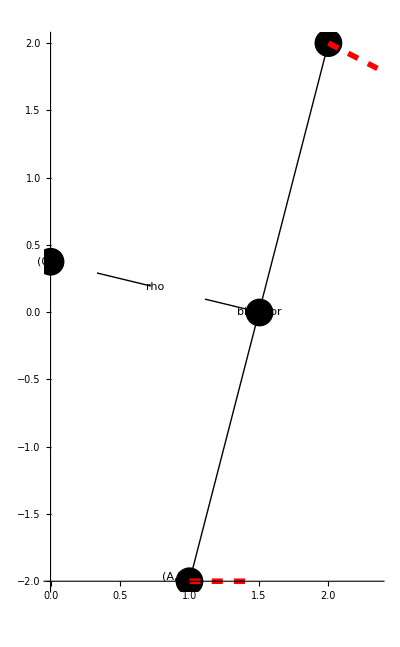

```mathematica
Show[picture]
```

## Stochastic dynamics of hinge location

Finally we examine the characteristics of the semimartingale Z

```mathematica
dZ=ItoD[Z];
0==Together[Drift[dZ]]/.localtimes
0==Together[ItoExpand[dZ^2]]
```

True

True

So Z doesn't move at all!

## Dynamics of distance between hinge and bisector

Just to finish off, we examine the distance rho between {0,Z} and the perpendicular bisector point. First we obtain the expression for rho from our previous solution of simultaneous linear equations:

```mathematica
rho=Simplify[rho/.solution]
```

-((A+X) √((A-X)^2+(B-Y)^2))/(2 (B-Y))

Now we compute its stochastic differential sd and its drift sd1. It is immediately clear that the drift is zero when the local time terms vanish, as the coefficient of dt is zero:

```mathematica
sd=ItoD[rho];
sd1=Expand[Together[Drift[sd]]];
0==Coefficient[sd1,dt]
```

True

So consider the coefficient of dL. Here we know A must be zero, as we interpret dL as the differential of the local time of A at zero:

```mathematica
0==Together[Coefficient[sd1,dL]-(X-A)/(4 rho)]/.A->0
```

True

Now consider the differential of dH. Similarly, here we know X must be zero, as we interpret dH as the differential of the local time of X at zero:

```mathematica
0==Together[Coefficient[sd1,dH]-(A-X)/(4 rho)]/.X->0
```

True

These last two calculations give us simpler forms for the drift of rho when either A or X is zero. We deduce the drift of rho is given in general by

```mathematica
driftdrho=((dL-dH) (X-A))/(4 rho)
```

-((-dH+dL) (-A+X) (B-Y))/(2 (A+X) √((A-X)^2+(B-Y)^2))

Here is a check. We know either dH, dL are both zero (off the boundary!)

```mathematica
0==Together[sd1-driftdrho]/.{dL->0,dH->0}
```

True

or X, dL are both zero (AA is on the axis X=0)

```mathematica
0==Together[sd1-driftdrho]/.{dL->0,X->0}
```

True

or dH, A are both zero (XX is on the axis X=0)

```mathematica
0==Together[sd1-driftdrho]/.{A->0,dH->0}
```

True

Now consider the second-order aspect of sd = ItoD[rho]. For some reason it is computationally burdensome to compute ItoExpand[sd^2] so we ease the task by noting that dA and dB generate the filtration. (Ignore the spelling warning!)

```mathematica
sd2a=Together[ItoExpand[sd dA]/dt]
sd2b=Together[ItoExpand[sd dB]/dt]
```

(-B+Y)/(√((A-X)^2+(B-Y)^2))

(A-X)/(√((A-X)^2+(B-Y)^2))

We deduce that rho behaves as a Brownian motion when XX and AA are away from the boundary: we have already computed the behaviour on the boundary!

```mathematica
1==Together[sd2a^2+sd2b^2]
```

True

So rho behaves as a standard Brownian motion with a singular drift imposed whenever one of the coupled Brownian motions hits the boundary.
As a further exercise, use Itovsn3 to compute the characteristics of the semimartingale given by the angle made by the bisector with the boundary.

## Contact Information

Email: w.s.kendall@warwick.ac.uk

URL: http://www.warwick.ac.uk/go/WSK

## Acknowledgements

The research reported here was supported by EPSRC grants GR/71677 (Stochastic calculus in AXIOM using modules of stochastic differentials) and GR/L56831 (Perfect simulation in stochastic geometry), and a joint EPSRC/BBSRC research grant (Multi-strain species modelling and control via differential algebra reductions). This Mathematica notebook was constructed on a visit to MSRI Berkeley CA during its 1997-1998 program Stochastic Analysis. Finally, it is a pleasure to express my gratitude to my friends Suzanne Scotchmer and Joseph Farrell for the generous hospitality they showed to me during my visit to MSRI.

## References

This calculation was a significant step in the following paper:

K.Burdzy and WSK: "Efficient Markovian Couplings: Examples and Counterexamples", in preparation (1998).

It also contributed usefully to:

R. Banuelos and K. Burdzy: "On the `hot spots' conjecture of J. Rauch", Preprint, Department of Mathematics, University of Washington (1997),

K. Burdzy and W. Werner: "A counterexample to the ``hot spots'' conjecture", Preprint, Department of Mathematics, University of Washington (1998).

Related Guides

Main

Related Tech Notes

Bessel

BlackScholes

ItoArea

MardiaDryden

StochasticIntegration

## Metadata

### Categorization

Tech Note

FernandoDuarte/Itovsn3

FernandoDuarte`Itovsn3`

FernandoDuarte/Itovsn3/tutorial/Reflect

### Keywords

Coupled Brownian motions, Reflected Brownian motion, Half-plane off a half-plane, Coupled by reflection